```mathematica
Guy F. Mongelli                                                                                  2/14/2013;
Prof. R.M. Sankaran                                                                      ECHE 462;
```

```mathematica
Group Assignment #2;
```

```mathematica
This assignment examines the series reaction of the following form for specific k1 and k2 values:
```

```mathematica
A(->)^Subscript[k, 1] B(->)^Subscript[k, 2] C
```

```mathematica
Problem#1;
```

```mathematica
First solve the general problem without specifying constants.
```

```mathematica
Clear[k1,k2,cA0,cA,cB,cC]
```

```mathematica
DSolve[{cA'[t]==-k1*cA[t],cA[0]==cA0},cA[t],t]
```

{{cA[t]→cA0 ⅇ^(-k1 t)}}

```mathematica
cA[t_]=cA0 ⅇ^(-k1 t)
```

cA0 ⅇ^(-k1 t)

```mathematica
DSolve[{cB'[t]==k1*cA[t]-k2*cB[t],cB[0]==0},cB[t],t]
```

{{cB[t]→-(cA0 ⅇ^(-(k1-k2) t-k2 t) (-1+ⅇ^((k1-k2) t)) k1)/(-k1+k2)}}

```mathematica
cB[t_]=-(cA0 ⅇ^(-(k1-k2) t-k2 t) (-1+ⅇ^((k1-k2) t)) k1)/(-k1+k2)
```

-(cA0 ⅇ^(-k2 t+(-k1+k2) t) (-1+ⅇ^((k1-k2) t)) k1)/(-k1+k2)

```mathematica
DSolve[{cC'[t]==k2*cB[t],cC[0]==0},cC[t],t]
```

{{cC[t]→(cA0 ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t) k1+ⅇ^(k1 t+k2 t) k1+ⅇ^(k2 t) k2-ⅇ^(k1 t+k2 t) k2))/(k1-k2)}}

```mathematica
cC[t_]=(cA0 ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t) k1+ⅇ^(k1 t+k2 t) k1+ⅇ^(k2 t) k2-ⅇ^(k1 t+k2 t) k2))/(k1-k2)
```

(cA0 ⅇ^(-k1 t-k2 t) (-ⅇ^(k1 t) k1+ⅇ^(k1 t+k2 t) k1+ⅇ^(k2 t) k2-ⅇ^(k1 t+k2 t) k2))/(k1-k2)

```mathematica
Defining the rate constants and initial concentration of species A, realizing that cA0 could be any value and the fractional conversions of that value as a function of time will be implied in the presently derived solution. The units of the rate constants could be any time variable.
```

```mathematica
cA0=1; (* moles/L *)
```

```mathematica
k1=.1; (* 1/time *)
```

```mathematica
k2=1; (* 1/time *)
```

```mathematica
Calling the functions cA,cB and cC with the specific Subscript[k, 1] and Subscript[k, 2] values:
```

```mathematica
cA[t]
```

ⅇ^(-0.1 t)

```mathematica
cB[t]
```

-0.111111 ⅇ^(-0.1 t) (-1+ⅇ^(-0.9 t))

```mathematica
cC[t]
```

-1.11111 ⅇ^(-1.1 t) (-0.1 ⅇ^(0.1 t)+ⅇ^t-0.9 ⅇ^(1.1 t))

```mathematica
The units of the rate constant are somewhat arbitrary in the sense that the time component could be arbitrarily selected (minutes, hours, days). However the order of the units in mass and volume are specified by the order of the reaction.
```

```mathematica
Then plot the concentration of each species as a function of time:
```

```mathematica
Needs["PlotLegends`"];
```

```mathematica
Plot[{cA[t],cB[t],cC[t]},{t,0,10},PlotRange->{0,1},PlotLegend->{"cA[t]","cB[t]","cC[t]"},AxesLabel->{"t","ci[t]"}]
```

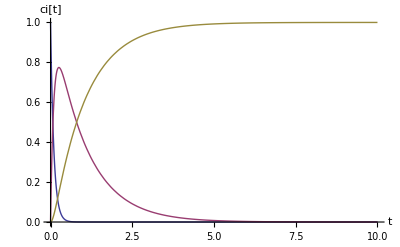

```mathematica
cA1[t_]=cA[t];
```

```mathematica
cB1[t_]=cB[t];
```

```mathematica
cC1[t_]=cC[t];
```

```mathematica
Problem 2:
```

```mathematica
Redefine the constants and apply them to the same solution:
```

```mathematica
k1=10;
```

```mathematica
k2=1;
```

```mathematica
cA[t]
```

ⅇ^(-10 t)

```mathematica
cB[t]
```

10/9 ⅇ^(-10 t) (-1+ⅇ^(9 t))

```mathematica
cC[t]
```

1/9 ⅇ^(-11 t) (ⅇ^t-10 ⅇ^(10 t)+9 ⅇ^(11 t))

```mathematica
Plot[{cA[t],cB[t],cC[t]},{t,0,10},PlotRange->{0,1},PlotLegend->{"cA[t]","cB[t]","cC[t]"},AxesLabel->{"t","ci[t]"}]
```

```mathematica
cA2[t]=cA[t];
```

```mathematica
cB2[t_]=cB[t];
```

```mathematica
cC2[t_]=cC[t];
```

```mathematica
Problem #3:
```

```mathematica
For the case of Subscript[k, 1]≃Subscript[k, 2], the form of the differential equation that governs the rate law of species B, and therefore C, are changed.  Therefore the form of the solution will be changed and is determined here:
```

```mathematica
Clear[cA,cB,cC,k1,k2,cA0]
```

```mathematica
DSolve[{cA'[t]==-k1*cA[t],cA[0]==cA0},cA[t],t]
```

{{cA[t]→cA0 ⅇ^(-k1 t)}}

```mathematica
cA[t_]=cA0 ⅇ^(-k1 t)
```

cA0 ⅇ^(-k1 t)

```mathematica
DSolve[{cB'[t]==k1*cA[t]-k1*cB[t],cB[0]==0},cB[t],t]
```

{{cB[t]→cA0 ⅇ^(-k1 t) k1 t}}

```mathematica
cB[t_]=cA0 ⅇ^(-k1 t) k1 t
```

cA0 ⅇ^(-k1 t) k1 t

```mathematica
DSolve[{cC'[t]==k2*cB[t],cC[0]==0},cC[t],t]
```

{{cC[t]→(cA0 ⅇ^(-k1 t) k2 (-1+ⅇ^(k1 t)-k1 t))/k1}}

```mathematica
cC[t_]=(cA0 ⅇ^(-k1 t) k2 (-1+ⅇ^(k1 t)-k1 t))/k1
```

(cA0 ⅇ^(-k1 t) k2 (-1+ⅇ^(k1 t)-k1 t))/k1

```mathematica
cA0=1;
```

```mathematica
k1=1;
```

```mathematica
k2=1;
```

```mathematica
cA[t]
```

ⅇ^-t

```mathematica
cB[t]
```

ⅇ^-t t

```mathematica
cC[t]
```

ⅇ^-t (-1+ⅇ^t-t)

```mathematica
Plot[{cA[t],cB[t],cC[t]},{t,0,10},PlotRange->{0,1},PlotLegend->{"cA[t]","cB[t]","cC[t]"},AxesLabel->{"t","ci[t]"}]
```

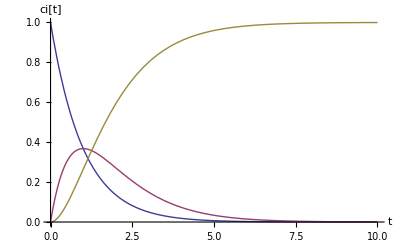

```mathematica
cA3[t]=cA[t];
```

```mathematica
cB3[t_]=cB[t];
```

```mathematica
cC3[t_]=cC[t];
```

```mathematica
Problem 4:
```

```mathematica
To determine the maximum concentrations of species B during the reaction for each rate constant ratio utilize the FindMaximum function:
```

```mathematica
The follwing concentrations are in moles/L:
```

```mathematica
FindMaximum[cB1[t],{t,1}]
```

{0.0774264,{t→2.55843}}

```mathematica
FindMaximum[cB2[t],{t,1}]
```

{0.774264,{t→0.255843}}

```mathematica
FindMaximum[cB3[t],{t,3}]
```

{0.367879,{t→1.}}

```mathematica
Problem 5:
```

```mathematica
Steady state is reached when the change in concentration of each species is constant with respect to time.   Equivalently, each of the cA[t], cB[t] or cC[t] could be examined. It is most convenient to utilize cB[t].
```

```mathematica
Plot[{cB1[t],cB2[t],cB3[t]},{t,0,15},PlotRange->{0,1},PlotLegend->{"cB1[t]","cB2[t]","cB3[t]"},AxesLabel->{"t","cBi[t]"}]
```

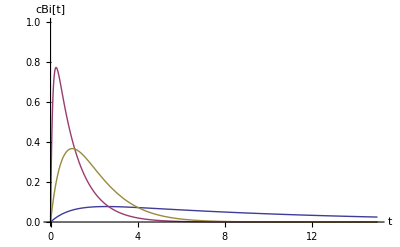

```mathematica
Arbitrarily specifying steady state to be acheived when cB[t] drops below .01 to the tenth place.  Again the time units are arbitrary.
```

```mathematica
cB1[24.5]
```

0.00958818

```mathematica
N[cB2[4.8],3]
```

0.00914416

```mathematica
N[cB3[6.5],3]
```

0.00977235

```mathematica
For the k1/k2=.1 case, S.S occurs at t=25.5(*time*).  For the k2/k1=10 case, S.S occurs at t=4.8 (*time*).  For the k2=k1 case, S.S. occurs at t=6.5 (*time*).
```